```mathematica
litmin1=0.00000002653;
litmax1=0.0000000282;
data1={0.0000481596056823373, 0.00000192668171379522, 0.0000481011420724916, 0.00000213993610656694, 0.0000474275071782782, 0.00000210707689893534, 0.0000305909273709289, 0.00000101641257234086, 0.0000044485894526704, 0.0000000774764951122332, 0.0000443416500202359, 0.00000109246845690182, 0.0000461611055229185, 0.000000197935780046936};
litmin2=0.00000001543;
litmax2=0.00000003;
data2={0.0000488516914335689, 0.00000174583952126622, 0.0000468798752020105, 0.00000206813973206971, 0.0000475866289091094, 0.00000172839031038585, 0.0000294845478275535, 0.000000755448010429187, 0.00000439742400969479, 0.000000112276754146326, 0.0000418686897514224, 0.00000101616700623747, 0.0000455033691487856, 0.000000103579779864518};
litmin3=0.00001431;
litmax3=0.0004854;
data3={0.0000752898142054594, 0.0000383492573317659, 0.0000683570575234166, 0.0000381913677125969, 0.0000675641322964496, 0.0000369207448056509, 0.000051732039693081, 0.0000260451383384849, 0.0000115381275901279, 0.00000404805955838926, 0.0000844843715962051, 0.0000310042714375077, 0.0000953812347567577, 0.0000243832499063448};
style={PlotStyle->{Red,PointSize[0.015]}};
xmin=-18.5;
xmax=-7;
```

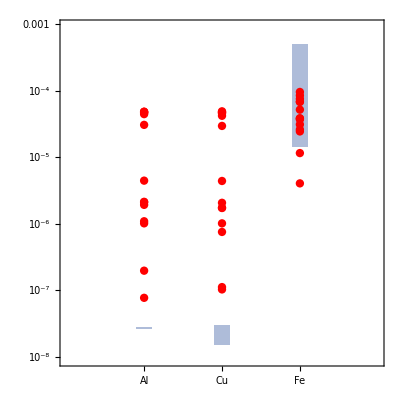

```mathematica
Show[ContourPlot[1,{x,0.9,1.1},{y,litmin1,litmax1},FrameTicks->{{All,None},{{{1,"Al"},{2,"Cu"},{3,"Fe"}},None}},ScalingFunctions->{None,"Log"},ColorFunction->"Aquamarine"],ContourPlot[1,{x,1.9,2.1},{y,litmin2,litmax2},ScalingFunctions->{None,"Log"},ColorFunction->"Aquamarine"],ContourPlot[1,{x,2.9,3.1},{y,litmin3,litmax3},ScalingFunctions->{None,"Log"},ColorFunction->"Aquamarine"],ListPlot[{1,#}&/@data1,style,ScalingFunctions->{None,"Log"}],ListPlot[{2,#}&/@data2,style,ScalingFunctions->{None,"Log"}],ListPlot[{3,#}&/@data3,style,ScalingFunctions->{None,"Log"}],PlotRange->{{0,4},{xmin,xmax}},Frame->True,FrameTicksStyle->24,Axes->False]
```